# AERO 628: Project 1 Prolate Rigid Body Rotation Mauricio Coen

## Angular Velocity Solution

The body has the following inertia matrix:

```mathematica
ⅈ=({{It, 0, 0}, {0, It, 0}, {0, 0, Ia}})
```

Set::wrsym: Symbol ⅈ is Protected.

{{It,0,0},{0,It,0},{0,0,Ia}}

And has a torque applied u:

```mathematica
u/It=0.2
```

Set::write: Tag Times in u/It is Protected.

0.2

Using Euler’s Eqs. of Motion: Since it is an axissymmetric-prolate body, the angular acceleration in the body-3 direction is zero.

```mathematica
Subscript[l, 3]=Ia OverDot[Subscript[ω, 3]]=0
```

Set::write: Tag Times in Ia OverDot[ω_3] is Protected.

0

So we can call ω_3=n which is a constant. Now simplifying the other expressions of Euler Eqs. of Motion:

```mathematica
Subscript[l, 2]=n Subscript[ω, 1] (It-Ia)+It OverDot[Subscript[ω, 2]]=0
OverDot[Subscript[ω, 2]]=(Ita-It)/It n Subscript[ω, 1]
```

Set::write: Tag Plus in (-Ia+It) n ω_1-It λ ω_1[0] is Protected.

0

((-It+Ita) n ω_1)/It

```mathematica
u=n Subscript[ω, 2] (Ia-It)+It OverDot[Subscript[ω, 1]]
 OverDot[Subscript[ω, 1]]=u/It+(It-Ia)/It n Subscript[ω, 2]
```

(Ia-It) n (-l/λ+b cos t λ+a sin t λ)+It (l+λ (-l/λ+b cos t λ+a sin t λ))

((-Ia+It) n (-l/λ+b cos t λ+a sin t λ))/It+((Ia-It) n (-l/λ+b cos t λ+a sin t λ)+It (l+λ (-l/λ+b cos t λ+a sin t λ)))/It

Now, we define the following expressions:

```mathematica
u/It≡l
λ≡(It-Ia)/It n
```

((Ia-It) n (-l/λ+b cos t λ+a sin t λ)+It (l+λ (-l/λ+b cos t λ+a sin t λ)))/It≡l

λ≡((-Ia+It) n)/It

```mathematica
OverDot[Subscript[ω, 1]]=λ Subscript[ω, 2]+l
OverDot[Subscript[ω, 2]]=-λ Subscript[ω, 1]
```

l+λ (-l/λ+b cos t λ+a sin t λ)

-λ ω_1

Differentiating the above and substituting:

```mathematica
Subscript[ω, 2]^(..)=-λ OverDot[Subscript[ω, 1]]
Subscript[ω, 2]^(..)+λ^2 Subscript[ω, 2]=λl
```

The differential equation can be solved by merging the homogeneous solution:

```mathematica
Subscript[w, 2 H]=a sin (λ t)+b cos (λ t)
```

b cos t λ+a sin t λ

With the particular solution:

```mathematica
Subscript[ω, 2P]=c,∴
```

```mathematica
c λ^2=λ l
c= -l/λ
```

Set::write: Tag Times in c λ^2 is Protected.

l λ

-l/λ

So the general solution is:

```mathematica
Subscript[ω, 2]=a sin (λ t)+b cos (λ t)-l/λ
```

-l/λ+b cos t λ+a sin t λ

Now we can differentiate when t=0 and plug into the OverDot[ω_2] equation:

```mathematica
OverDot[Subscript[ω, 2]]=a cos (λ t(0))-b sin (λ t(0))=-λ Subscript[ω, 1](0)
a=-λ Subscript[ω, 1](0)
Subscript[ω, 2](0)=b cos (λ t(0))-l/λ+(-λ) Subscript[ω, 1](0) sin (λ t(0))
b=l/λ+Subscript[ω, 2](0)
```

Set::write: Tag Plus in a cos λ t[0]-b sin λ t[0] is Protected.

-λ ω_1[0]

-λ ω_1[0]

Set::write: Tag Plus in (-l/λ+b cos t λ-sin t λ^2 ω_1[0])[0] is Protected.

-l/λ+b cos λ t[0]-sin λ^2 t[0] ω_1[0]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of l/λ.

Hold[l/λ+(-l/λ+b cos t λ-sin t λ^2 ω_1[0])[0]]

## Orientation Angles Solution

Using a 1-2-3 (α , β, γ) rotation sequence, we get the following attitude kinematics matrix:

(α̇
β̇
γ̇)=1/Cos[β] (Cos[γ]
Cos[β] Sin[γ]
-Sin[β]  Cos[γ]-Sin[γ] | 0
Cos[γ] Cos[β]
Sin[γ] Sin[β] | 0
Cos[β])(ω_1
ω_2
ω_3)

```mathematica
R1=({{1, 0, 0}, {0, cos(α), sin(α)}, {0, -sin(α), cos(α)}});
R2=({{cos(β), 0, -sin(β)}, {0, 1, 0}, {sin(β), 0, cos(β)}});
R3=({{cos(γ), sin(γ), 0}, {-sin(γ), cos(γ), 0}, {0, 0, 1}});
ω={Subscript[ω, 1],Subscript[ω, 2],Subscript[ω, 3]};
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of l/λ.

```mathematica
A={0,0,Subscript[ω, 3]}+R3.{0,Subscript[ω, 2],0}+R3.R2.{Subscript[ω, 1],0,0}//MatrixForm
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of l/λ.

Hold[A={0,0,ω_3}+R3.{0,ω_2,0}+R3.R2.{ω_1,0,0}]

Notice that γ̇ can be simplified in the following way:

```mathematica
γ̇=n-tan(β) (Subscript[ω, 1] cos(γ)-Subscript[ω, 2] sin(γ))
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of l/λ.

Hold[γ̇=n-Tan[β] (ω_1 Cos[γ]-ω_2 Sin[γ])]

Substituting for α̇ in the equation above:

```mathematica
γ̇=n-α̇ sin(β)
```

n-α̇ Sin[β]

Since we have a prolate body, we can approximate the orientation angles solution with small angle approximations, where Cos[β] ≈ 1 and Sin[β] ≈ β:

```mathematica
∴
```

```mathematica
α̇=Subscript[ω, 1] cos(γ)-Subscript[ω, 2] sin(γ)
β̇=Subscript[ω, 1] sin(γ)+Subscript[ω, 2] cos(γ)
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of l/λ.

Hold[α̇=ω_1 Cos[γ]-ω_2 Sin[γ]]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of l/λ.

Hold[β̇=ω_1 Sin[γ]+ω_2 Cos[γ]]

```mathematica
ClearAll["Global`*"]
```

#### Matlab numerical Integration

```mathematica
y=Import["/home/mau/workspace/y.mat"]
time=Flatten[Import["/home/mau/workspace/t.mat"]];
```

{{{0.,0.,0.,0.,0.,5.},{0.0000250974,6.99064×10^-7,0.0792447,0.00316683,-0.00011925,5.},1414,{-0.124376,0.167083,150.109,-0.0380423,-0.0601164,5.}}}
 |  |  |  |

```mathematica
y1= y[[1,All]];
```

```mathematica
αnum=Flatten[y1[[All,1]]];
βnum=     y1[[All,2]];
ω1num= y1[[All,4]];
ω2num= y1[[All,5]];
```

```mathematica
alplot=Transpose[{time,αnum}];
beplot=Transpose[{time,βnum}];
ome1=Transpose[{time,ω1num}];
ome2=Transpose[{time,ω2num}];
```

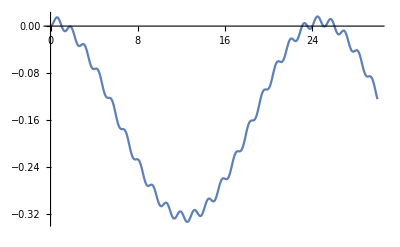

```mathematica
ListLinePlot[alplot]
```

#### equation that Hurtado gave:

```mathematica
αHur=l/(λ n)(1-Cos[n t]) - l It/(λ Ia n) (1-Cos[Ia/It n t ])
```

(l (1-Cos[n t]))/(n λ)-(It l (1-Cos[(Ia n t)/It]))/(Ia n λ)

```mathematica
alpha1=αHur/.{λ->(It-Ia)/It n,l->0.2}
```

(0.2 It (1-Cos[n t]))/((-Ia+It) n^2)-(0.2 It^2 (1-Cos[(Ia n t)/It]))/(Ia (-Ia+It) n^2)

```mathematica
alphaHurtado=alpha1/.{It->1,Ia->0.05,n->5}
```

-0.168421 (1-Cos[0.25 t])+0.00842105 (1-Cos[5 t])

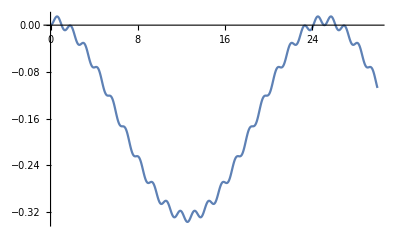

```mathematica
Plot[alphaHurtado,{t,0,30}]
```

#### Wolfram analytical integration

```mathematica
α̇=Subscript[ω, 1] Cos[γ]-Subscript[ω, 2] Sin[γ]
```

-(-l/λ+b cos t λ+a sin t λ) Sin[γ]+Cos[γ] ω_1

```mathematica
omega1=(l/λ) Sin[λ t]
omega2=(l/λ) Cos[λ t]-l/λ
```

(l Sin[t λ])/λ

-l/λ+(l Cos[t λ])/λ

```mathematica
Clear[n]
```

```mathematica
alphaSubs=α̇/.{Subscript[ω, 1]->omega1,Subscript[ω, 2]->omega2,γ->n t}
```

-(-l/λ+(l Cos[t λ])/λ) Sin[n t]+(l Cos[n t] Sin[t λ])/λ

```mathematica
alphaPreInt=Simplify[alphaSubs=α̇/.{Subscript[ω, 1]->omega1,Subscript[ω, 2]->omega2,γ->n t}]
```

(2 l Cos[n t-(t λ)/2] Sin[(t λ)/2])/λ

```mathematica
alphaW=Simplify[Integrate[alphaPreInt,t]]/.{λ->(It-Ia)/It n}
```

(It l (-Cos[n t]/n+Cos[(n-((-Ia+It) n)/It) t]/(n-((-Ia+It) n)/It)))/((-Ia+It) n)

```mathematica
Simplify[alphaW]
```

(It l (Ia Cos[n t]-It Cos[(Ia n t)/It]))/(Ia (Ia-It) n^2)

```mathematica
alphaPlot=alphaW/.{l->0.2,It->1,Ia->0.05}
```

(0.210526 ((20. Cos[0.05 n t])/n-Cos[n t]/n))/n

```mathematica
Simplify[alphaPlot]
```

(4.21053 Cos[0.05 n t]-0.210526 Cos[n t])/n^2

```mathematica
Clear[n,t]
```

```mathematica
Evaluate[alphaPlot/.t->0]
```

0.16

```mathematica
NumberForm[0.16,16]
```

0.16

```mathematica
Plot[alphaPlot-0.16,{t,0,30}]
```

-Graphics-

#### Beta

```mathematica
β̇=Subscript[ω, 1] Sin[γ]+Subscript[ω, 2] Cos[γ]
```

(-l/λ+b cos t λ+a sin t λ) Cos[γ]+Sin[γ] ω_1

```mathematica
omega1=(l/λ) Sin[λ t];
omega2=(l/λ) Cos[λ t]-l/λ;
```

```mathematica
betaSubs=β̇/.{Subscript[ω, 1]->omega1,Subscript[ω, 2]->omega2,γ->n t}
```

Cos[n t] (-l/λ+(l Cos[t λ])/λ)+(l Sin[n t] Sin[t λ])/λ

```mathematica
betaPreInt=Simplify[betaSubs=β̇/.{Subscript[ω, 1]->omega1,Subscript[ω, 2]->omega2,γ->n t}]
```

(2 l Sin[(t λ)/2] Sin[n t-(t λ)/2])/λ

```mathematica
betaW=Simplify[Integrate[betaPreInt,t]]/.{λ->(It-Ia)/It n}
```

(It l (-Sin[n t]/n+Sin[(n-((-Ia+It) n)/It) t]/(n-((-Ia+It) n)/It)))/((-Ia+It) n)

```mathematica
Simplify[betaW]
```

(It l (Ia Sin[n t]-It Sin[(Ia n t)/It]))/(Ia (Ia-It) n^2)

```mathematica
betaPlot=betaW/.{l->0.2,It->1,Ia->0.05}
```

(0.210526 ((20. Sin[0.05 n t])/n-Sin[n t]/n))/n

```mathematica
Evaluate[betaPlot/.t->0]
```

0.

```mathematica
NumberForm[0.16,16]
```

0.16

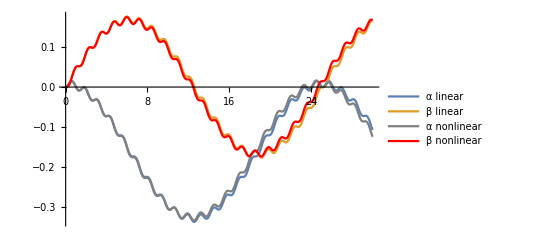

```mathematica
Show[Plot[{Legended[alphaPlot-0.16,"α linear" ],Legended[betaPlot,"β linear"]},{t,0,30}], ListLinePlot[Legended[alplot,"α nonlinear"],PlotStyle->Gray],ListLinePlot[Legended[beplot,"β nonlinear"],PlotStyle->Red]]
```

```mathematica
n = 1000;
per = 12.34;
pdata = Table[Sin[2 π x/per], {x,n}] + RandomReal[.1,{n}]
Dimensions[pdata]
ListPlot[pdata];
```

{1000}

```mathematica
Dimensions[beplot[[All,2]]]
```

{1417}

```mathematica
beplot[[All,2]];
```

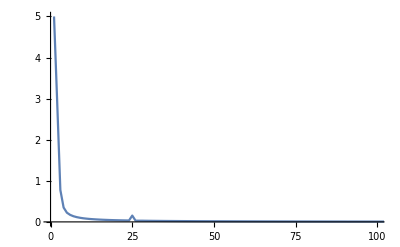

```mathematica
ListLinePlot[Abs[Fourier[alplot[[All,2]]]],PlotRange->{{0,100},{0,5}}]
```

```mathematica
ArrowsDeltaFunction[eqn_,x_]:=Module[{xsubs,listDeltas,coefDeltas,locationDeltas},xsubs=(x/.Cases[eqn,DiracDelta[a__]:>Solve[a==0,x],Infinity])/.x->{};
listDeltas=DiracDelta[x-x0]/.x0->xsubs;
coefDeltas=Flatten[Coefficient[eqn,listDeltas]];
locationDeltas=Flatten[xsubs];
Arrow[Table[{{locationDeltas[[i]],0},{locationDeltas[[i]],coefDeltas[[i]]}},{i,1,Length[locationDeltas]}]]]
```

```mathematica
alphaPlot
```

0.0421053 (4. Cos[0.25 t]-1/5 Cos[5 t])

```mathematica
Fo=FourierTransform[alphaPlot,t,p,FourierParameters->{0, -2*Pi}]
```

0.52911 DiracDelta[(0.25+0. ⅈ)-2 p π]-0.0264555 DiracDelta[5-2 p π]+0.52911 DiracDelta[(0.25+0. ⅈ)+2 p π]-0.0264555 DiracDelta[5+2 p π]

```mathematica
Abs[Fo]
```

Abs[(0.-0.52911 ⅈ) DiracDelta[(0.25+0. ⅈ)-2 p π]+(0.+0.0264555 ⅈ) DiracDelta[5-2 p π]+(0.+0.52911 ⅈ) DiracDelta[(0.25+0. ⅈ)+2 p π]-(0.+0.0264555 ⅈ) DiracDelta[5+2 p π]]

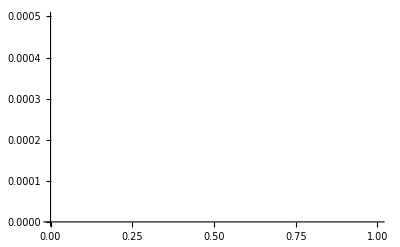

```mathematica
Plot[Fo,{p,0,5},PlotStyle->{Thick,Red},Epilog->{Thick,Red,ArrowsDeltaFunction[Fo,p]},PlotRange->{{0,1},{0,0.0005}}]
```

```mathematica
Evaluate@Abs[Fo]
```

Abs[(0.-0.52911 ⅈ) DiracDelta[(0.25+0. ⅈ)-2 p π]+(0.+0.0264555 ⅈ) DiracDelta[5-2 p π]+(0.+0.52911 ⅈ) DiracDelta[(0.25+0. ⅈ)+2 p π]-(0.+0.0264555 ⅈ) DiracDelta[5+2 p π]]

```mathematica
Plot[Evaluate@Abs[Fo],{p,1*^-1,1*^1},PlotRange->Full]
```

-Graphics-

```mathematica
FourierTransform[Sin[10 t]+Cos[t],t,ω]
LogLogPlot[Evaluate@Abs[%],{ω,1*^-1,1*^5},PlotRange->All]
```

ⅈ √(π/2) DiracDelta[-10+ω]+√(π/2) DiracDelta[-1+ω]+√(π/2) DiracDelta[1+ω]-ⅈ √(π/2) DiracDelta[10+ω]

-Graphics-

```mathematica
0.796 0.05
```

0.0398